/Users/zack/Documents/ignition/cantera/ratematrix

{{2,9,0.1},{3,19,0.2},{4,48,1.2},{5,89,8.9},{6,177,69.8},{7,298,452.4}}

{{3,19,0.2},{4,48,1.},{5,89,5.1},{6,177,34.2},{7,298,156.3},{8,516,738.7}}

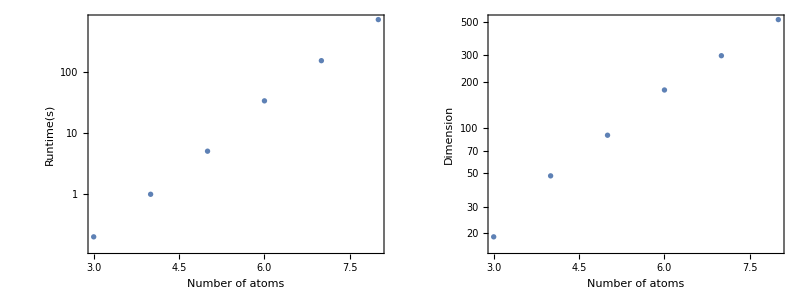

logplot.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
dat={{2,9,0.1},{3,19,0.2},{4,48,1.2},{5,89,8.9},{6,177,69.8},{7,298,452.4}}
dat={{3,19,0.2},{4,48,1.0},{5,89,5.1},{6,177,34.2},{7,298,156.3},{8,516,738.7}}
p=Grid[{{ListLogPlot[dat[[All,{1,3}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListLogPlot[dat[[All,{1,2}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]}}]
Export["logplot.pdf",p]
```